```mathematica
Ylm[l_,m_,θ_,ϕ_]:=LegendreP[l,m,Cos[θ]] Exp[I m ϕ] (-1)^m
Rlm[l_,m_,r_,θ_,ϕ_]:=(-1)^m r^l/(l+m)! Ylm[l,m,θ,ϕ];
Slm[l_,m_,r_,θ_,ϕ_]:=(-1)^m (l-m)!/r^(l+1) Ylm[l,m,θ,ϕ];
vec[r_,θ_,ϕ_]:={r Sin[θ] Cos[ϕ],r Sin[θ] Sin[ϕ],r Cos[θ]}
spher[x_,y_,z_]:={Sqrt[x^2+y^2+z^2],ArcCos[z/Sqrt[x^2+y^2+z^2]],ArcTan[x,y]}
myWignerD[{j_,m1_,m2_},α_,β_,ɣ_]:=WignerD[{j,-m1,-m2},α,β,ɣ];
(*Klm={0,kr22+I ki22, kr21+I ki21, k20,-kr21+I ki21, kr22-I ki22,0};*)
Klm={0,0.02,0,-0.1,0,0.02,0};
G=(3.98199*10^14)/M;
```

```mathematica
EulerMatrix[{Pi/2,Pi/2,γ}].{0,0,1}
```

{0,1,0}

```mathematica
complextorque=(*(G M)/2*)Sum[Sum[Conjugate[Slm[2,mp,r,θ,ϕ]](-1)^2 Sqrt[((2-mpp)!(2+mpp)!)/((2-mp)!(2+mp)!)]Conjugate[myWignerD[{2,mp,mpp},a,b,c]]({I,-1,0} (2-mpp+1)Klm[[mpp-1+4]]+{I,1,0}(2+mpp+1)Klm[[mpp+1+4]]+2 {0,0,I}mpp Klm[[mpp+4]]),{mpp,-2,2}],{mp,-2,2}];
complextorque/.{r->3.18124*10^08,θ->Pi/2,ϕ->1.86989, a->-2.6573,b->  2.45539,c-> 2.78244}//MatrixForm
```

(-2.27033×10^-27+0. ⅈ
-2.91531×10^-27+0. ⅈ
-1.24237×10^-26+0. ⅈ)

(-(0.389018 Cos[a] Sin[a])/r^3
(1.41367 Cos[a] Sin[a])/r^3
(0.218231-0.218231 Cos[2 a])/r^3)

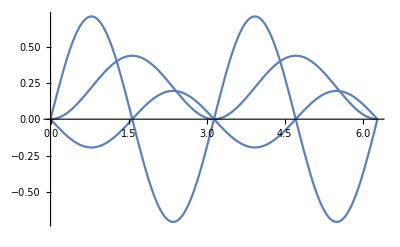

```mathematica
Simplify[ExpToTrig[complextorque/.{a->a,b->Pi/2,c->1,θ->Pi/2,ϕ->0}], Assumptions->{r>0,γ>0, ϕ>0,a>0,b>0}]//MatrixForm
Plot[complextorque/.{a->a,b->Pi/2,c->1,θ->Pi/2,ϕ->0, r->1},{a,0,2Pi}]
```

```mathematica
simptorque=Simplify[G m M/(2 RD^3) am^2  Sum[Sqrt[(2-mpp)!]Sqrt[(2+mpp)!]Conjugate[myWignerD[{2,0,mpp},a,b,c]]
({I,-1,0}(2-mpp+1)Klm[[mpp-1+4]]+{I,1,0}(2+mpp+1)Klm[[mpp+1+4]]+2{0,0,I}mpp Klm[[mpp+4]]),{mpp,-2,2}], Assumptions->{b>0, a>0, c>0}];
simptorque/(m am^2)
```

{-((0.+3.58379×10^13 ⅈ) ⅇ^(-ⅈ c) (-1.+1. ⅇ^(2 ⅈ c)) Sin[2 b])/RD^3,(2.5×10^-7 ⅇ^(-ⅈ c) (3.34487×10^20+3.34487×10^20 ⅇ^(2 ⅈ c)) Sin[2 b])/RD^3,((0.+4.77839×10^13 ⅈ) ⅇ^(-2 ⅈ c) (-1.+1. ⅇ^(4 ⅈ c)) Sin[b]^2)/RD^3}

```mathematica
Keq =Simplify[ Solve[Ixx==2/3 m am^2(k20-6kr22+1)&& Iyy==2/3 m am^2(k20+6kr22+1)&&Izz==2/3 m am^2(-2k20+1)&& Ixy==-2/3 m am^2(6 ki22)&& Ixz==2/3 m am^2(3kr21)&& Iyz==2/3 m am^2(3 ki21),{kr22, ki22, kr21, ki21,k20, am},Reals, Assumptions->{m>0, Ixx>0, Iyy>0,Izz>0,am>0}]][[1]]
```

{kr22→(-Ixx+Iyy)/(4 (Ixx+Iyy+Izz)),ki22→-Ixy/(2 (Ixx+Iyy+Izz)),kr21→Ixz/(Ixx+Iyy+Izz),ki21→Iyz/(Ixx+Iyy+Izz),k20→(Ixx+Iyy-2 Izz)/(2 (Ixx+Iyy+Izz)),am→(√((Ixx+Iyy+Izz)/m))/(√2)}

```mathematica
itorque=Simplify[simptorque/.Keq];
itorque//MatrixForm
```

(-(3 ⅇ^(-2 ⅈ c) G M (-2 ⅇ^(2 ⅈ c) Iyz+6 ⅇ^(2 ⅈ c) Iyz Cos[b]^2+(ⅈ (-1+ⅇ^(4 ⅈ c)) Ixz+(1+ⅇ^(4 ⅈ c)) Iyz) Sin[b]^2+ⅇ^(ⅈ c) ((1+ⅇ^(2 ⅈ c)) Ixy-ⅈ (-1+ⅇ^(2 ⅈ c)) (Iyy-Izz)) Sin[2 b]))/(4 RD^3)
(3 ⅇ^(-2 ⅈ c) G M (2 ⅇ^(2 ⅈ c) Ixz-6 ⅇ^(2 ⅈ c) Ixz Cos[b]^2+((1+ⅇ^(4 ⅈ c)) Ixz-ⅈ (-1+ⅇ^(4 ⅈ c)) Iyz) Sin[b]^2+ⅇ^(ⅈ c) (-((1+ⅇ^(2 ⅈ c)) Ixx)+ⅈ (-1+ⅇ^(2 ⅈ c)) Ixy+(1+ⅇ^(2 ⅈ c)) Izz) Sin[2 b]))/(4 RD^3)
-(3 ⅈ ⅇ^(-2 ⅈ c) G M ((-1+ⅇ^(4 ⅈ c)) Ixx-2 ⅈ Ixy-2 ⅈ ⅇ^(4 ⅈ c) Ixy+Iyy-ⅇ^(4 ⅈ c) Iyy+2 ⅇ^(ⅈ c) ((-1+ⅇ^(2 ⅈ c)) Ixz-ⅈ (1+ⅇ^(2 ⅈ c)) Iyz) Cot[b]) Sin[b]^2)/(4 RD^3))

```mathematica
Rz[a_]:={{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}};
Ry[a_]:={{Cos[a],0,Sin[a]},{0,1,0},{-Sin[a],0,Cos[a]}};
R=Rz[-c].Ry[-b].Rz[-a];
Ig=Transpose[R].{{Ixx,Ixy,Ixz},{Ixy,Iyy,Iyz},{Ixz,Iyz,Izz}}.R;
firsttorque=(3 G M)/RD^3{-Ig[[3,2]],Ig[[3,1]],0}
```

{1/RD^3 3 G M (-((Cos[b] Cos[c] Sin[a]+Cos[a] Sin[c]) (Ixz Cos[b]-Ixx Cos[c] Sin[b]+Ixy Sin[b] Sin[c]))-(Cos[a] Cos[c]-Cos[b] Sin[a] Sin[c]) (Iyz Cos[b]-Ixy Cos[c] Sin[b]+Iyy Sin[b] Sin[c])-Sin[a] Sin[b] (Izz Cos[b]-Ixz Cos[c] Sin[b]+Iyz Sin[b] Sin[c])),1/RD^3 3 G M ((Cos[a] Cos[b] Cos[c]-Sin[a] Sin[c]) (Ixz Cos[b]-Ixx Cos[c] Sin[b]+Ixy Sin[b] Sin[c])+(-Cos[c] Sin[a]-Cos[a] Cos[b] Sin[c]) (Iyz Cos[b]-Ixy Cos[c] Sin[b]+Iyy Sin[b] Sin[c])+Cos[a] Sin[b] (Izz Cos[b]-Ixz Cos[c] Sin[b]+Iyz Sin[b] Sin[c])),0}

```mathematica
Simplify[((R).(firsttorque/.{Ixz->-Ixz, Ixy->-Ixy})-ComplexExpand[itorque])]
```

{0,0,0}

```mathematica
explicit={a->2,b->1,c->3,Ixx->0.4,Iyy->0.3,Izz->0.29,Ixy->0,Ixz->0,Iyz->0,RD->20,G->1,M->1};
R.firsttorque/.explicit
itorque/.explicit
```

{-2.406×10^-7,0.0000185666,-3.70963×10^-6}

{-2.406×10^-7+6.61744×10^-23 ⅈ,0.0000185666+0. ⅈ,-3.70963×10^-6-1.34946×10^-21 ⅈ}